### Problem 1

#### Normalizing P

```mathematica
Integrate[4 π n Exp[-2a r^2]r^2,{r,0,Infinity}]
```

ConditionalExpression[(n π^(3/2))/(2 √2 a^(3/2)),Re[a]>0]

```mathematica
Solve[(n π^(3/2))/(2 √2 a^(3/2))==1, n]
```

{{n→(2 √2 a^(3/2))/π^(3/2)}}

#### Calculating HPsi / Psi

```mathematica
Sqrt[(2 √2 a^(3/2))/π^(3/2)Exp[-2a r^2]]
```

√(a^(3/2) ⅇ^(-2 a r^2)) (2/π)^(3/4)

```mathematica
Psi[r_]:=a^(3/4) ⅇ^(-a r^2) (2/π)^(3/4)
```

```mathematica
Simplify[
(-(1/2)*Laplacian[Psi[r],{r,θ,ϕ},"Spherical"]-Psi[r]/r)
/Psi[r]
]
```

3 a-1/r-2 a^2 r^2

#### Analytical Solution

```mathematica
Integrate[
4π r^2 *
Psi[r]*(-(1/2)*Laplacian[Psi[r],{r,θ,ϕ},"Spherical"]-Psi[r]/r),
{r,0,Infinity}
]
```

ConditionalExpression[-(√a (8-3 √a √(2 π)))/(2 √(2 π)),Re[a]>0]

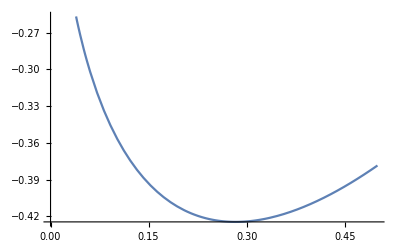

```mathematica
var1ana=Plot[-(√a (8-3 √a √(2 π)))/(2 √(2 π)),{a,0,0.5}]
```

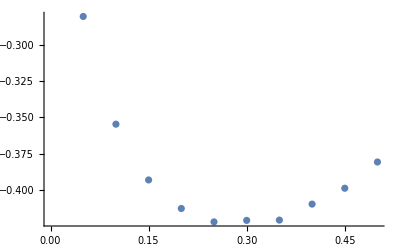

```mathematica
var1=ListPlot[{{.050000000000000003,-0.28055641456155150},
{0.10000000000000001,-0.35467765956884928 },
{0.15000000000000002,-0.39304232911834525 },
{0.20000000000000001,-0.41268362788177032 },
{0.25000000000000000,-0.42190810520768102 },
{0.30000000000000004,-0.42087687833643916 },
{0.35000000000000003,-0.42066778077257200 },
{0.40000000000000002,-0.40966247563136493 },
{0.45000000000000001,-0.39874763905692512 },
{0.50000000000000000,-0.38069646033320770}}]
```

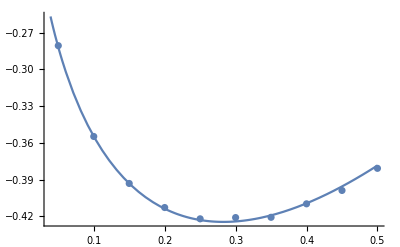

```mathematica
Show[var1,var1ana,PlotRange->Automatic]
```

```mathematica
Solve[D[-(√a (8-3 √a √(2 π)))/(2 √(2 π)),a]==0]
```

{{a→8/(9 π)}}

```mathematica
ReplaceAll[-(√a (8-3 √a √(2 π)))/(2 √(2 π)),{a->8/(9 π)}]
```

-4/(3 π)

### Problem 2

#### Finding HPsi/Psi

```mathematica
PsiP2[r_]:=Exp[-a r]
```

```mathematica
Expand[Simplify[(-(1/2)*Laplacian[PsiP2[r],{r,θ,ϕ},"Spherical"]-PsiP2[r]/r)/PsiP2[r]]]
```

-a^2/2-1/r+a/r

#### Analytical soln

```mathematica
Integrate[
4π r^2 *
PsiP2[r]*(-(1/2)*Laplacian[PsiP2[r],{r,θ,ϕ},"Spherical"]-PsiP2[r]/r),
{r,0,Infinity}
]
```

ConditionalExpression[((-2+a) π)/(2 a^2),Re[a]>0]

```mathematica
var2ana=Plot[((-2+a) π)/(2 a^2),{a,0,2}]
```

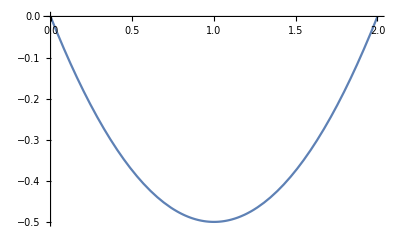

```mathematica
var3ana=Plot[a^2/2-a,{a,0,2}]
```

```mathematica
var2=ListPlot[{{.050000000000000003,-0.28055641456155150},
{0.10000000000000001,-0.35467765956884928 },
{0.15000000000000002,-0.39304232911834525 },
{0.20000000000000001,-0.41268362788177032 },
{0.25000000000000000,-0.42190810520768102 },
{0.30000000000000004,-0.42087687833643916 },
{0.35000000000000003,-0.42066778077257200 },
{0.40000000000000002,-0.40966247563136493 },
{0.45000000000000001,-0.39874763905692512 },
{0.50000000000000000,-0.38069646033320770}}]
```

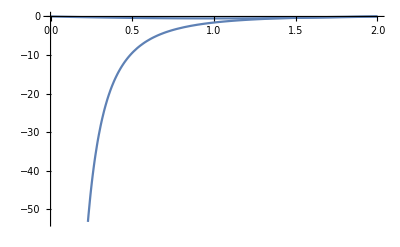

```mathematica
Show[var2ana,var3ana]
```

### Problem 3

#### Finding <H> without electron repulsion term

```mathematica
PsiP3[r1_,r2_]:=Exp[-a r1]Exp[-a r2]
```

```mathematica
Integrate[
(
(-1/2)(Laplacian[PsiP3[r1,r2],{r1,θ,ϕ},"Spherical"]+Laplacian[PsiP3[r1,r2],{r2,θ,ϕ},"Spherical"])
-2(1/r1+1/r2)PsiP3[r1,r2]
)* PsiP3[r1,r2]*(4π)^2* r1^2*r2^2
,
{r1,0,Infinity},{r2,0,Infinity}
]
```

ConditionalExpression[((-4+a) π^2)/a^5,Re[a]>0]

#### Finding repulsion term